```mathematica
(*  Guy F. Mongelli                               ChE 400
   Prof. Clark                                   9/17/2010     *)

(*Assignment #3
Problem #1     *)
```

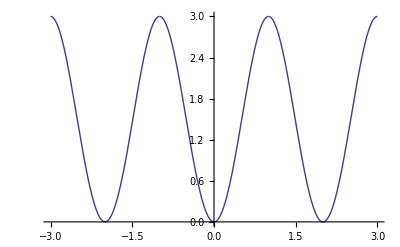

```mathematica
L=1;
fbas[x_]:=7x^2-5x^4+x^6
f[x_]:=fbas[Mod[x,2×L,-L]];
Plot[f[x],{x,-3,3}]
```

```mathematica
(* The Convergence Guideline discussed in class indicates that if the kth derivative is peicewise continuous in the extended function (1 discontinuity per period), the the fourier corefficients will drop off as the inverse of n to the k+1 power. In the case of this function, k is the fifth derivative.  Therefore, I expect the fourier coefficients to drop off as 1/n to the sixth  *)
```

```mathematica
(* Problem #2*)
```

```mathematica
a[0]=1/(2 L)∫_-L^L f[x]ⅆx
```

31/21

```mathematica
a[n_]=Simplify[1/L∫_-L^L f[x]Cos[(n π x)/L]ⅆx,n∈Integers]
```

(1440 (-1)^n)/(n^6 π^6)

```mathematica
b[n_]=Simplify[1/L∫_-L^L f[x]Sin[(n π x)/L]ⅆx,n∈Integers]
```

0

```mathematica
coeffs=Table[{a[i],b[i]},{i,1,20}];
TableForm[coeffs]
```

-1440/π^6 | 0
45/(2 π^6) | 0
-160/(81 π^6) | 0
45/(128 π^6) | 0
-288/(3125 π^6) | 0
5/(162 π^6) | 0
-1440/(117649 π^6) | 0
45/(8192 π^6) | 0
-160/(59049 π^6) | 0
9/(6250 π^6) | 0
-1440/(1771561 π^6) | 0
5/(10368 π^6) | 0
-1440/(4826809 π^6) | 0
45/(235298 π^6) | 0
-32/(253125 π^6) | 0
45/(524288 π^6) | 0
-1440/(24137569 π^6) | 0
5/(118098 π^6) | 0
-1440/(47045881 π^6) | 0
9/(400000 π^6) | 0

```mathematica
fs[k_,x_]:=coeffs[[k,1]]*Cos[k*Pi*x/L]+coeffs[[k,2]]*Sin[k*Pi*x/L]
```

```mathematica
fourier[n_,x_]:=a[0]+∑_(k=1)^n fs[k,x]
```

```mathematica
fourier[5,x]
```

31/21-(1440 Cos[π x])/π^6+(45 Cos[2 π x])/(2 π^6)-(160 Cos[3 π x])/(81 π^6)+(45 Cos[4 π x])/(128 π^6)-(288 Cos[5 π x])/(3125 π^6)

```mathematica
fourier[10,x]
```

31/21-(1440 Cos[π x])/π^6+(45 Cos[2 π x])/(2 π^6)-(160 Cos[3 π x])/(81 π^6)+(45 Cos[4 π x])/(128 π^6)-(288 Cos[5 π x])/(3125 π^6)+(5 Cos[6 π x])/(162 π^6)-(1440 Cos[7 π x])/(117649 π^6)+(45 Cos[8 π x])/(8192 π^6)-(160 Cos[9 π x])/(59049 π^6)+(9 Cos[10 π x])/(6250 π^6)

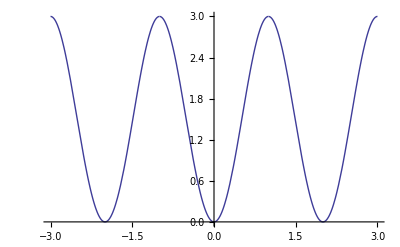

```mathematica
graphone=Plot[f[x],{x,-3,3},Exclusions->{-1,1}]
```

```mathematica
(*Manipulate[  consider manipulating k to find a reasonable value*)
```

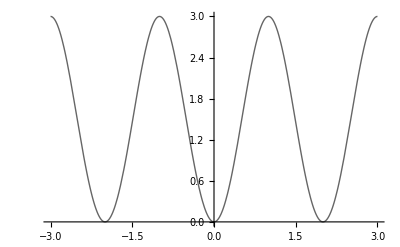

```mathematica
graphtwo=Plot[fourier[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

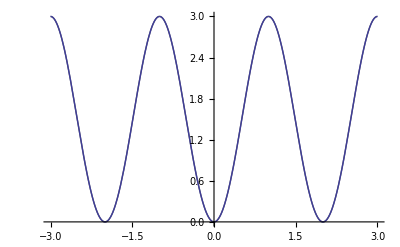

```mathematica
bothtwo=Show[graphtwo,graphone]
```

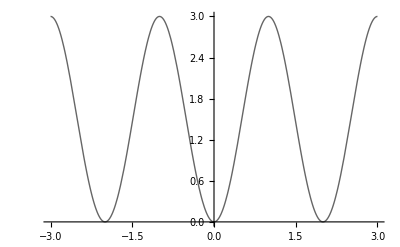

```mathematica
graphthree=Plot[fourier[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

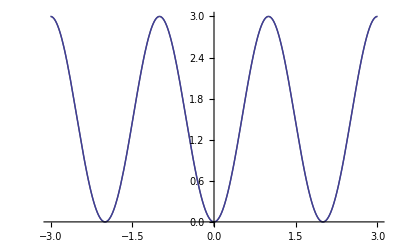

```mathematica
boththree=Show[graphthree,graphone]
```

```mathematica
graphsix=Plot[fourier[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]];
```

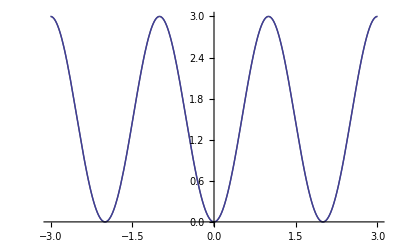

```mathematica
bothsix=Show[graphsix,graphone]
```

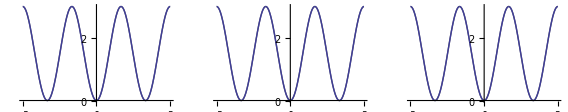

```mathematica
Show[GraphicsRow[{bothtwo,boththree,bothsix}]]
```